```mathematica
f[x_, y_, ε_, Iext_] := 1/ε * (x - 1/3*x^3 - y + Iext)
g[x_, y_, a_, b_] := x + a - b*y

J[x_, ε_] := ({{(1-x^2)/ε, -1/ε}, {1, -b}})
```

```mathematica
a = 1;
b = 1;
ε = 1/100;
```

```mathematica
xrange = 3;
yrange = 3;
Irange = 1;

Manipulate[
	Show[
		StreamPlot[{f[x,y,ε,Iext], g[x,y,a,b]}, {x, -xrange, xrange}, {y, -yrange, yrange},
		StreamStyle -> Automatic,
		StreamColorFunction -> "Rainbow",
		FrameLabel -> {"x", "y"},
		StreamPoints -> Fine,
		AspectRatio -> 1]
	],
{Iext,0,Irange}]
```

```mathematica
(Sqrt[99]/10)^3/3;
1-0.328346
```

0.671654

```mathematica
maxt = 5;
sol[x0_, y0_, Iext_] := NDSolve[{x'[t] == 1/ε * (x[t] - 1/3*x[t]^3 - y[t] + Iext), y'[t] == x[t] + a - b*y[t], x[0]==x0,y[0]==y0},
								{x,y},
								{t,0,maxt}]
nullclinesX[x_, Iext_] := x - 1/3 * x^3 + Iext;
nullclinesY[x_] := x + 1;
```

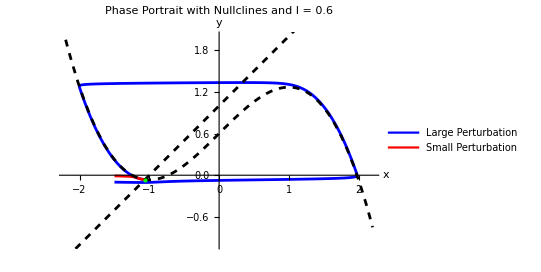

```mathematica
initialConditions = {
  {-1.5, -0.1},  
  {-1.5, -0.01}
};
numberOfConditions = Length[initialConditions];
colors = {Blue, Red};
labels = {"Large Perturbation", "Small Perturbation"};

minx=-2.2;
miny=-1;
maxx=2.2;
maxy=2;

Iext = 0.6;
fixedX = -1.06265857;
fixedY = fixedX + 1;
p1 = ParametricPlot[
  Evaluate[
    Table[
      {x[t], y[t]} /. sol[initialConditions[[i, 1]], initialConditions[[i, 2]], Iext],
      {i, 1, numberOfConditions}
    ]
  ],
  {t, 0, maxt},
  PlotRange -> {{minx, maxx}, {miny, maxy}},
  AxesLabel -> {"x", "y"},
  PlotStyle -> colors,
  PlotLegends -> LineLegend[colors, labels],
  PlotLabel -> "I = " <> ToString[Iext],
  Method -> {"Arrowheads" -> Medium}
];

(* Plot Nullclines *)
nullclineXPlot = Plot[
  nullclinesX[x, Iext],
  {x, minx, maxx},
  PlotStyle -> {Dashed, Black},
  PlotLegends -> None
];

nullclineYPlot = Plot[
  nullclinesY[x],
  {x, minx, maxx},
  PlotStyle -> {Dashed, Black},
  PlotLegends -> None
];

finalPlot = Show[
  p1,
  nullclineXPlot,
  nullclineYPlot,
  Graphics[{
    Green,
    PointSize[Large],
    Point[{fixedX, fixedY}]
  }],
  PlotRange -> {{minx, maxx}, {miny, maxy}},
  AxesLabel -> {"x", "y"},
  PlotLabel -> "Phase Portrait with Nullclines and I = 0.6"
  
];


finalPlot
```

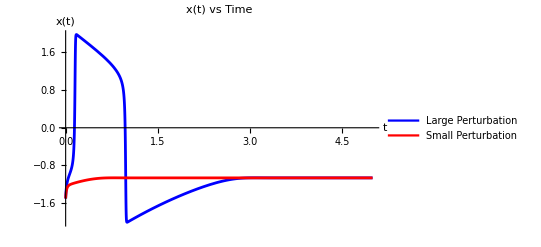

```mathematica
solutions = Table[
  sol[initialConditions[[i, 1]], initialConditions[[i, 2]], Iext],
  {i, 1, numberOfConditions}
];

xSolutions = Table[
  x[t] /. solutions[[i]],
  {i, 1, numberOfConditions}
];

timePlot = Plot[
  Evaluate[xSolutions],
  {t, 0, maxt},
  PlotRange -> All,
  PlotStyle -> colors,
  AxesLabel -> {"t", "x(t)"},
  PlotLegends -> Placed[LineLegend[colors, labels], Above],
  PlotLabel -> "x(t) vs Time",
  ImageSize -> 400
]
```